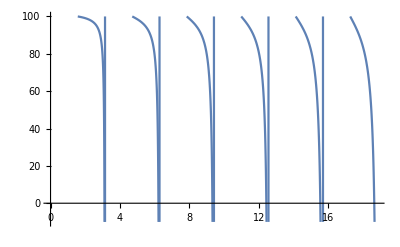

{k→3.141278525747552}

{k→6.282557051557091}

{k→9.42383557749061}

{k→12.56511410361008}

{k→15.70639262997751}

{k→18.84767115665487}

{k→21.98894968370416}

{k→25.13022821118736}

{k→28.27150673916645}

```mathematica
Clear[KL]
Plot[KL+ k Cot[k]/. KL -> 100., {k,0,6π}, PlotRange -> {-10, 100}]
For[n=1,n<10,n++,Print[NumberForm[FindRoot[KL+k Cot[k]/. KL -> 10000., {k, n*π*.99999}], 20]]]
```

```mathematica
"3.141278525747552"^2
6.27690848113237^2
9.41536287609952^2
"28.27150673916645"^2
```

9.86763

39.3996

88.6491

799.278